## EdgesUsed-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 09:14:32
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

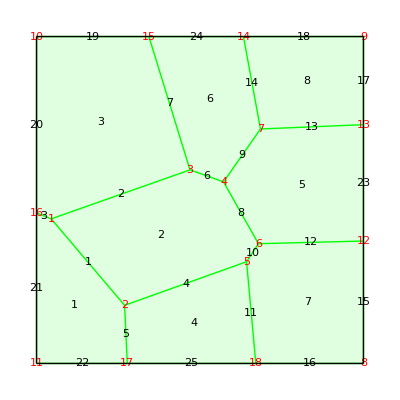

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

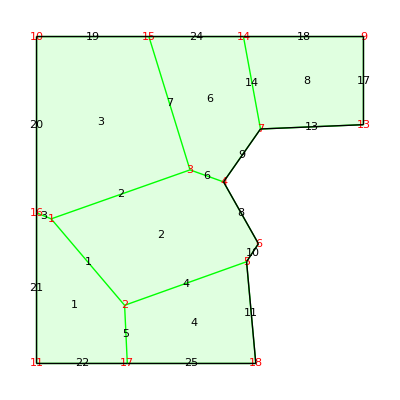

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

Now use the “All” option to show the edges and vertices that are NOT part of any cell

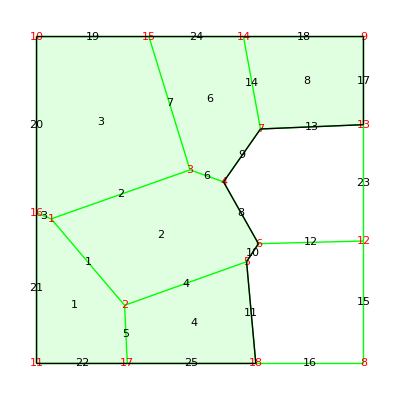

```mathematica
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12], 
"All"-> True]
```

```mathematica
R
```

DTissue[{{-45.5206,-5.76459},{-23.0655,-32.2099},{-3.0605,9.21244},{7.20239,5.5376},{14.2444,-18.8804},{17.8739,-13.3677},{18.5032,21.724},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-12.5506},{50.,23.0417},{13.2868,50.},{-15.6339,50.},{-50.,-3.92739},{-22.2342,-50.},{17.0749,-50.}},{{1,2},{1,3},{1,16},{2,5},{2,17},{3,4},{3,15},{4,6},{4,7},{5,6},{5,18},{6,12},{7,13},{7,14},{8,12},{8,18},{9,13},{9,14},{10,15},{10,16},{11,16},{11,17},{12,13},{14,15},{17,18}},{1→{22,5,1,3,21},2→{1,4,10,8,6,2},3→{20,3,2,7,19},4→{25,11,4,5},6→{24,7,6,9,14},8→{18,14,13,17}}]

```mathematica
TissueEdges[R]
```

{{1,2},{1,3},{1,16},{2,5},{2,17},{3,4},{3,15},{4,6},{4,7},{5,6},{5,18},{6,12},{7,13},{7,14},{8,12},{8,18},{9,13},{9,14},{10,15},{10,16},{11,16},{11,17},{12,13},{14,15},{17,18}}

Find the edges that are used:

```mathematica
EdgesUsed[R]
```

{1,2,3,4,5,6,7,8,9,10,11,13,14,17,18,19,20,21,22,24,25}

Find the edges that still exist in the tissue but are not used:

```mathematica
Complement[Range[NTissueEdges[R]], EdgesUsed[R]]
```

{12,15,16,23}

Find the vertices that are used

```mathematica
VerticesUsed[R]
```

{1,2,3,4,5,6,7,9,10,11,13,14,15,16,17,18}

Find the Vertices that remain in R that are not used:

```mathematica
Complement[Range[NTissueVertices[R]], VerticesUsed[R]]
```

{8,12}